```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep2.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

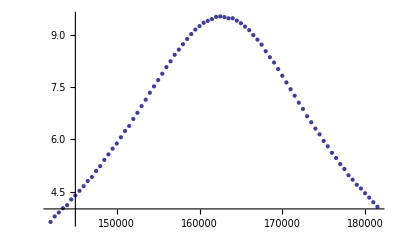

```mathematica
dataplot=ListPlot[plotdata]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

42{162500.,9.53}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,{model,150000<x0<170000},{x0,g,b},x,MaxIterations->10000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 10000 iterations. The best estimated solution, with feasibility residual, KKT residual or complementary residual of {1.17267×10^-8, 0.000612492, 5.86338×10^-9}, is returned.

NonlinearRegress::constr: The report values {ANOVATable, AsymptoticCorrelationMatrix, EstimatedVariance, FitCurvatureTable, ParameterCITable} assume an unconstrained model. The results for these report values may not be valid, particularly if the fitted parameters are near a constraint boundary.

{BestFitParameters→{x0→152395.,g→146.359,b→97.0575},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 152395. | 3.17997×10^6 | {-6.17973×10^6,6.48452×10^6}
g | 146.359 | 322938. | {-642905.,643198.}
b | 97.0575 | 428998. | {-854146.,854340.},EstimatedVariance→52.1032,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 0.251504 | 0.0838347
Error | 77 | 4011.94 | 52.1032
Uncorrected Total | 80 | 4012.2 | 
Corrected Total | 79 | 279.791 | ,AsymptoticCorrelationMatrix→(1. | -0.000146592 | -0.0003585
-0.000146592 | 1. | 0.00208969
-0.0003585 | 0.00208969 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 5398.25
Max Parameter-Effects | 6939.86
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

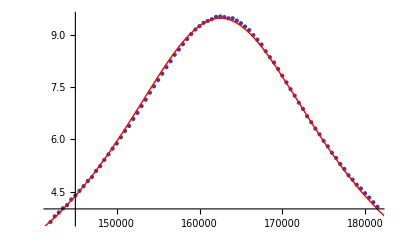

```mathematica
Show[dataplot,fitplot]
```